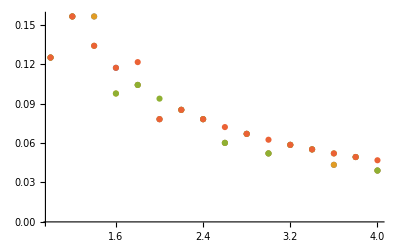

```mathematica
b11={{1,6/(1×32)}, {1.2,13/(1.2×32)},{1.4,20/(1.4×32)},{1.6,26/(1.6×32)}, {1.8,33/(1.8×32)},{2,39/(2×32)},{2.2,46/(2.2×32)},{2.4,53/(2.4×32)},{2.6,59/(2.6×32)},{2.8,66/(2.8×32)},{3,72/(3×32)},{3.2,79/(3.2×32)},{3.4,85/(3.4×32)},{3.6,91/(3.6×32)},{3.8,98/(3.8×32)},{4,104/(4×32)}};
b21={{1,9/(1×32)}, {1.2,15/(1.2×32)},{1.4,22/(1.4×32)},{1.6,28/(1.6×32)}, {1.8,35/(1.8×32)},{2,41/(2×32)},{2.2,48/(2.2×32)},{2.4,55/(2.4×32)},{2.6,61/(2.6×32)},{2.8,68/(2.8×32)},{3,74/(3×32)},{3.2,81/(3.2×32)},{3.4,87/(3.4×32)},{3.6,93/(3.6×32)},{3.8,100/(3.8×32)},{4,106/(4×32)}};
b31={{1,12/(1×32)}, {1.2,18/(1.2×32)},{1.4,24/(1.4×32)},{1.6,30/(1.6×32)}, {1.8,37/(1.8×32)},{2,44/(2×32)},{2.2,50/(2.2×32)},{2.4,57/(2.4×32)},{2.6,63/(2.6×32)},{2.8,70/(2.8×32)},{3,76/(3×32)},{3.2,83/(3.2×32)},{3.4,89/(3.4×32)},{3.6,96/(3.6×32)},{3.8,102/(3.8×32)},{4,108/(4×32)}};
b41={{1,15/(1×32)}, {1.2,21/(1.2×32)},{1.4,27/(1.4×32)},{1.6,33/(1.6×32)}, {1.8,40/(1.8×32)},{2,46/(2×32)},{2.2,53/(2.2×32)},{2.4,59/(2.4×32)},{2.6,66/(2.6×32)},{2.8,72/(2.8×32)},{3,79/(3×32)},{3.2,85/(3.2×32)},{3.4,91/(3.4×32)},{3.6,98/(3.6×32)},{3.8,104/(3.8×32)},{4,111/(4×32)}};
b12={{1,2/(1×32)}, {1.2,7/(1.2×32)},{1.4,13/(1.4×32)},{1.6,20/(1.6×32)}, {1.8,27/(1.8×32)},{2,34/(2×32)},{2.2,40/(2.2×32)},{2.4,47/(2.4×32)},{2.6,54/(2.6×32)},{2.8,60/(2.8×32)},{3,67/(3×32)},{3.2,73/(3.2×32)},{3.4,79/(3.4×32)},{3.6,86/(3.6×32)},{3.8,92/(3.8×32)},{4,99/(4×32)}};
b22={{1,5/(1×32)}, {1.2,9/(1.2×32)},{1.4,15/(1.4×32)},{1.6,23/(1.6×32)}, {1.8,29/(1.8×32)},{2,36/(2×32)},{2.2,42/(2.2×32)},{2.4,49/(2.4×32)},{2.6,56/(2.6×32)},{2.8,62/(2.8×32)},{3,69/(3×32)},{3.2,75/(3.2×32)},{3.4,81/(3.4×32)},{3.6,88/(3.6×32)},{3.8,94/(3.8×32)},{4,101/(4×32)}};
b32={{1,8/(1×32)}, {1.2,12/(1.2×32)},{1.4,18/(1.4×32)},{1.6,25/(1.6×32)}, {1.8,31/(1.8×32)},{2,38/(2×32)},{2.2,44/(2.2×32)},{2.4,51/(2.4×32)},{2.6,58/(2.6×32)},{2.8,64/(2.8×32)},{3,71/(3×32)},{3.2,77/(3.2×32)},{3.4,83/(3.4×32)},{3.6,90/(3.6×32)},{3.8,96/(3.8×32)},{4,103/(4×32)}};
b42={{1,11/(1×32)}, {1.2,15/(1.2×32)},{1.4,21/(1.4×32)},{1.6,27/(1.6×32)}, {1.8,33/(1.8×32)},{2,41/(2×32)},{2.2,47/(2.2×32)},{2.4,53/(2.4×32)},{2.6,60/(2.6×32)},{2.8,66/(2.8×32)},{3,73/(3×32)},{3.2,79/(3.2×32)},{3.4,85/(3.4×32)},{3.6,92/(3.6×32)},{3.8,98/(3.8×32)},{4,105/(4×32)}};
b1=b11-b12*Table[{0,1},{i,0,15}];
b2=b21-b22*Table[{0,1},{i,0,15}];
b3=b31-b32*Table[{0,1},{i,0,15}];
b4=b41-b42*Table[{0,1},{i,0,15}];
ListPlot[{b1,b2,b3,b4}]
```

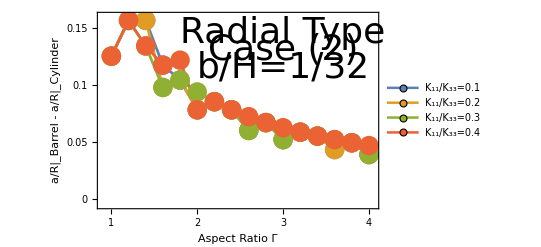

```mathematica
ListPlot[{b1,b2,b3,b4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0,0.05,0.1,0.15},None},{{0,1,2,3,4},None}}, PlotRange->{{0.9,4.05},{-0.005,0.16}},FrameLabel->{{"a/R|_Barrel - a/R|_Cylinder", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Radial Type",Directive[Black,36]],{3.0,0.145}],Text[Style["Case (2)",Directive[Black,36]],{3.0,0.13}],
Text[Style["b/H=1/32",Directive[Black,36]],{3.0,0.115}]}]
```